## 1) Logistic equation

Here we will explore the  logistic equation dn/dt=rn(1-n/k)=f(n)

### Plot dn/dt vs n.

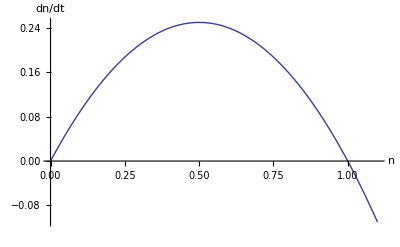

```mathematica
r=1.0;
k=1.0;
n0=0.1;

f[n_]:=r*n*(1-n/k);

Plot[f[n],{n,0,1.1},AxesLabel->{"n","dn/dt"}]
```

### Solve the model numerically for different initial conditions.

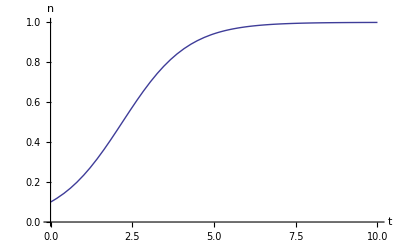

```mathematica
tmax=10;

sol=NDSolve[{n'[t]==f[n[t]],n[0]==n0},n,{t,0,tmax}];

Plot[n[t]/.sol,{t,0,tmax},AxesLabel->{"t","n"}]
```

### Now we'll move to analytical mode, so let's clear out those particular parameter values.

```mathematica
Clear[r,k]
```

### Find equilibria.

```mathematica
eq=Solve[f[n]==0,n]
```

{{n→0},{n→k}}

### Analyse their stability.

```mathematica
(* calculate slope *)

df=D[f[n],n]
```

-(n r)/k+(1-n/k) r

```mathematica
(* evaluate at equilibrium 1 *)

df/.eq[[1]]
```

r

```mathematica
(* evaluate at equilibrium 2 *)

df/.eq[[2]]
```

-r

## 2) Allee effects

Now do the same for a model with an Allee effect: dn/dt=r*(n-a)*(k-n)*n, 0<a<k

0.5

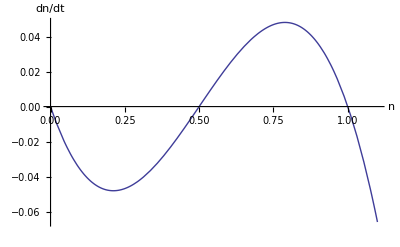

```mathematica
Clear[r, k]
r=1.0;
k=1.0;
n0=0.1;
a = 0.5

f[n_]:=r*(n-a)*(k-n)*n

Plot[f[n],{n,0,1.1},AxesLabel->{"n","dn/dt"}]
```

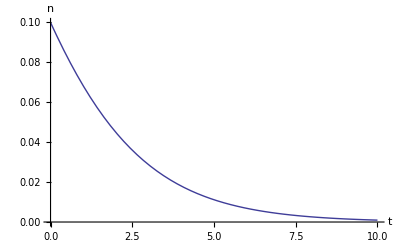

```mathematica
tmax=10;

sol=NDSolve[{n'[t]==f[n[t]],n[0]==n0},n,{t,0,tmax}];

Plot[n[t]/.sol,{t,0,tmax},AxesLabel->{"t","n"}]
```

```mathematica
Clear[r, k, a]
eq=Solve[f[n]==0,n]
```

{{n→0},{n→a},{n→k}}

```mathematica
df=D[f[n],n]
```

(k-n) n r+(k-n) (-a+n) r-n (-a+n) r

```mathematica
df/.eq[[1]]
```

-a k r

## 3) Discrete-time logistic exploration

Here we will further explore the discrete logistic equation discussed in class and in May (1974): n[t+1]=n[t]exp[r*(1-n[t]/k)].

#### Simulate the difference equation for r=1.0,1.4,1.8,2.2,2.6,3.0.

```mathematica
Clear[n,f];

(* set parameters *)

r=2.8;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,0,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]
```

#### At what value of r do 2-cycles begin? Investiagate the transition between a stable equilibrium and a 2-cycle by slowly raising r through this critical value. Simulate the model (ie, copy the above code and paste it down here) and also plot n[t+2] vs n[t] to see the birth of the 2-cycle using the code below.

```mathematica
Plot[{n,f[f[n]]},{n,0,2},PlotRange->{0,2},AxesLabel->{"n[t]","n[t+2]"}]
```

#### Investiagate the transition between a 2-cycle and a 4-cycle by slowly raising r through r=2.526. Simulate the model and also plot n[t+4] vs n[t] using the code below.

```mathematica
Plot[{n,f[f[f[f[n]]]]},{n,0,2},PlotRange->{0,2},AxesLabel->{"n[t]","n[t+4]"}]
```

#### One hallmark of chaos is "sensitive dependence on inital conditions". This means that if you run two copies of the exact same equation with slightly different initial densities, the two diverge over time. Demonstrate sensitive dependence on initial conditions for r=3.0, and the lack of it for r=2.6 by simultaneously solving two identical difference equations with slightly different initial conditions, then plotting the difference between the solutions. Why do chaotic populations diverge then converge again?

```mathematica
Clear[n,f];

(* set parameters *)

r=2.6;
n[0]=0.1;
m[0]=0.10001;
tmax=100;
f[n_]=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
n[t+1]=f[n[t]];
m[t+1]=f[m[t]];
	,{t,0,tmax}];

(* plot n[t], m[t], and n[t]-m[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","n[t]"}]
ListPlot[Table[m[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","m[t]"}]
ListPlot[Table[n[t]-m[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","n[t]-m[t]"}]
```

#### A bifurcation diagram is a convenient summary of how a model depends on its parameters. Make one for the discrete logistic map, plotting the population densities reached as a function of r.

```mathematica
tmax=200;

(* solve the difference equation for values of r between 0 and 4 stepping by 0.01 *)

Do[
	   n[0,r]=1.01;
     Do[
	        n[t+1,r]=n[t,r]*E^(r*(1-n[t,r]));
	 ,{t,0,tmax}];
,{r,1.0,4.0,0.01}]

(* plot the final 100 points for each r *)

ListPlot[Flatten[Table[{r,n[t,r]},{r,1.0,4.0,0.01},{t,tmax-100,tmax}],1]]
```

#### Notice the "windows" in the chaotic region, such as the one around r=3.12. What type of solution is occurs for this range of r? Simulate the difference equation and see. What happens as r increases? Note: the cobwebbing code below plots only the last 30 years of data to eliminate the transient dynamics that would obscure the long-term behavior.

```mathematica
Clear[n,f];

(* set parameters *)

r=3.12;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,tmax-30,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]
```